# Exploring Nontrivial Ising Spin Topologies

Here, we attempt to understand the statistical mechanics of Ising-spin models on Cayley Graph topologies.

## Section 1 | Coding the Partition Function:

## Section 1.1 | The Partition Function:

```mathematica
PartitionFunctionForIsingSpins[Hamiltonian_,n_Integer,OptionsPattern[{"Verbose"->False}]]:=Module[{SymbolicSpinVariables,PartitionFunctionSymbolicForm,PartitionFunctionNumerical,MicroscopicConfigurations,i=0},
(*Define the spins as s[i] symbols*)
SymbolicSpinVariables=Table[s[i],{i,1,n}];

(*Construct symbolic Boltzmann factor*)
PartitionFunctionSymbolicForm=Exp[-β*Hamiltonian];

If[OptionValue["Verbose"],
Print["> Symbolic partition function: Z = ",PartitionFunctionSymbolicForm];
];

(*Generate all spin configurations:each s[i]∈{-1,1}*)
MicroscopicConfigurations=Tuples[{-1,1},n];

(*Sum the Boltzmann factor over all configurations*)
PartitionFunctionNumerical=Total[(i++;
If[OptionValue["Verbose"],
Print["> Summing configuration #",i,": ",#]
];
PartitionFunctionSymbolicForm/. Thread[SymbolicSpinVariables->#])&/@MicroscopicConfigurations];

PartitionFunctionNumerical
]
```

```mathematica
CalculateAverageEnergy[PartitionFunction_]:=-D[Log[PartitionFunction],β];
```

```mathematica
CalculateVarianceEnergy[PartitionFunction_]:=D[Log[PartitionFunction],{β,2}];
```

```mathematica
CalculateFreeEnergy[PartitionFunction_]:=-Log[PartitionFunction]/β;
```

```mathematica
CalculateEntropy[PartitionFunction_]:=Log[PartitionFunction]+β CalculateAverageEnergy[PartitionFunction];
```

## Section 2 | Standard Examples:

## Section 2.1 | 1D Ising Chain with N=4:

## Section 2.1.1 | Hamiltonian:

```mathematica
Hamiltonian1DIsingChainN4=-J (s[1] s[2]+s[2] s[3]+s[3] s[4])
```

-J (s[1] s[2]+s[2] s[3]+s[3] s[4])

## Section 2.1.2 | Partition Function:

```mathematica
Z1DIsingChainN4=PartitionFunctionForIsingSpins[Hamiltonian1DIsingChainN4,4,"Verbose"->False]//FullSimplify
```

16 Cosh[J β]^3

## Section 2.1.3 | Average Energy:

```mathematica
CalculateAverageEnergy[Z1DIsingChainN4]//FullSimplify
```

-3 J Tanh[J β]

## Section 2.1.4 | Energy Variance:

```mathematica
CalculateVarianceEnergy[Z1DIsingChainN4]//FullSimplify
```

3 J^2 Sech[J β]^2

## Section 2.1.5 | Free Energy:

```mathematica
CalculateFreeEnergy[Z1DIsingChainN4]//FullSimplify
```

-Log[16 Cosh[J β]^3]/β

## Section 2.2 | 1D Ising Ring with N=4:

## Section 2.2.1 | Hamiltonian:

```mathematica
Hamiltonian1DIsingRingN4=-(s[1] s[2]+s[2] s[3]+s[3] s[4]+s[1] s[4])
```

-s[1] s[2]-s[2] s[3]-s[1] s[4]-s[3] s[4]

## Section 2.2.2 | Partition Function:

```mathematica
Z1DIsingRingN4=PartitionFunctionForIsingSpins[Hamiltonian1DIsingRingN4,4,"Verbose"->False]//FullSimplify
```

4 (3+Cosh[4 β])

## Section 2.2.3 | Average Energy:

```mathematica
CalculateAverageEnergy[Z1DIsingRingN4]//FullSimplify
```

-(4 Sinh[4 β])/(3+Cosh[4 β])

## Section 2.2.4 | Energy Variance:

```mathematica
CalculateVarianceEnergy[Z1DIsingRingN4]//FullSimplify
```

(16 (1+3 Cosh[4 β]))/(3+Cosh[4 β])^2

## Section 2.2.5 | Free Energy:

```mathematica
CalculateFreeEnergy[Z1DIsingRingN4]//FullSimplify
```

-Log[4 (3+Cosh[4 β])]/β

## Section 2.3 | 1D Ising Chain with N=10:

## Section 2.3.1 | Hamiltonian

```mathematica
Hamiltonian1DIsingChainN10=-J (s[1] s[2]+s[2] s[3]+s[3] s[4]+s[4]s[5]+s[5]s[6]+s[6]s[7]+s[7]s[8]+s[8]s[9]+s[9]s[10])
```

-J (s[1] s[2]+s[2] s[3]+s[3] s[4]+s[4] s[5]+s[5] s[6]+s[6] s[7]+s[7] s[8]+s[8] s[9]+s[9] s[10])

## Section 2.3.2 | Partition Function:

```mathematica
Z1DIsingChainN10=PartitionFunctionForIsingSpins[Hamiltonian1DIsingChainN10,10,"Verbose"->False]//FullSimplify
```

1024 Cosh[J β]^9

## Section 2.3.3 | Average Energy:

```mathematica
CalculateAverageEnergy[Z1DIsingChainN10]//FullSimplify
```

-9 J Tanh[J β]

## Section 2.3.4 | Energy Variance:

```mathematica
CalculateVarianceEnergy[Z1DIsingChainN10]//FullSimplify
```

9 J^2 Sech[J β]^2

## Section 2.3.5 | Free Energy:

```mathematica
CalculateFreeEnergy[Z1DIsingChainN10]//FullSimplify
```

-Log[1024 Cosh[J β]^9]/β

## Section 2.4 | 1D Ising Ring with N=10:

## Section 2.4.1 | Hamiltonian

```mathematica
Hamiltonian1DIsingRingN10=-J (s[1] s[2]+s[2] s[3]+s[3] s[4]+s[4]s[5]+s[5]s[6]+s[6]s[7]+s[7]s[8]+s[8]s[9]+s[9]s[10]+s[10]s[1]);
```

## Section 2.4.2 | Partition Function:

```mathematica
Z1DIsingRingN10=PartitionFunctionForIsingSpins[Hamiltonian1DIsingRingN10,10,"Verbose"->False]//FullSimplify
```

4 (210 Cosh[2 J β]+45 Cosh[6 J β]+Cosh[10 J β])

## Section 2.4.3 | Average Energy:

```mathematica
CalculateAverageEnergy[Z1DIsingRingN10]//FullSimplify
```

-(8 J (22 Sinh[4 J β]+Sinh[8 J β]))/(83+44 Cosh[4 J β]+Cosh[8 J β])-2 J Tanh[2 J β]

## Section 2.4.4 | Energy Variance:

```mathematica
CalculateVarianceEnergy[Z1DIsingRingN10]//FullSimplify
```

(40 J^2 (6235+7704 Cosh[4 J β]+2268 Cosh[8 J β]+168 Cosh[12 J β]+9 Cosh[16 J β]))/(210 Cosh[2 J β]+45 Cosh[6 J β]+Cosh[10 J β])^2

## Section 2.4.5 | Free Energy:

```mathematica
CalculateFreeEnergy[Z1DIsingRingN10]//FullSimplify
```

-Log[4 (210 Cosh[2 J β]+45 Cosh[6 J β]+Cosh[10 J β])]/β

## Section 3 | Exotic Examples:

## Section 3.0 | Ising-Like Spins for Cayley Graph of S_2

## Section 3.0.1 | Generating the Cayley Graph of S_2

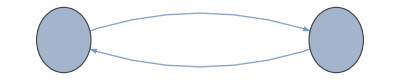

```mathematica
CayleyGraph[SymmetricGroup[2],VertexLabels->Placed["Name",Center],VertexSize->0.2]
```

## Section 3.0.2 | Hamiltonian

```mathematica
HamiltonianCayleyGraphS2=-J(
s[1]s[2]
)
```

-J s[1] s[2]

## Section 3.0.3 | Partition Function:

```mathematica
ZCayleyGraphS2=PartitionFunctionForIsingSpins[HamiltonianCayleyGraphS2,2,"Verbose"->False]//FullSimplify
```

4 Cosh[J β]

## Section 3.0.4 | Average Energy:

```mathematica
AvgEnergyCayleyGraphS2=CalculateAverageEnergy[ZCayleyGraphS2]//FullSimplify
```

-J Tanh[J β]

## Section 3.0.5 | Energy Variance:

```mathematica
EnergyVarCayleyGraphS2=CalculateVarianceEnergy[ZCayleyGraphS2]//FullSimplify
```

J^2 Sech[J β]^2

## Section 3.0.6 | Free Energy:

```mathematica
FreeECayleyGraphS2=CalculateFreeEnergy[ZCayleyGraphS2]//FullSimplify
```

-Log[4 Cosh[J β]]/β

## Section 3.0.7 | Entropy:

```mathematica
SCayleyGraphS2=CalculateEntropy[ZCayleyGraphS2]//FullSimplify
```

Log[4 Cosh[J β]]-J β Tanh[J β]

## Section 3.1 | Ising-Like Spins for Cayley Graph of S_3

## Section 3.1.1 | Generating the Cayley Graph of S_3

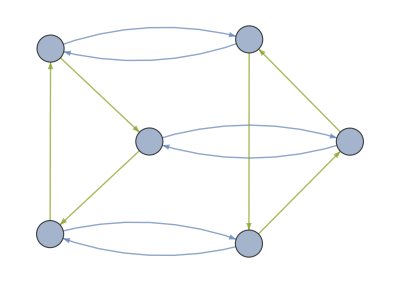

```mathematica
CayleyGraph[SymmetricGroup[3],VertexLabels->Placed["Name",Center],VertexSize->0.2]
```

## Section 3.1.2 | Hamiltonian:

```mathematica
HamiltonianCayleyGraphS3=-J(
s[1]s[3]+s[1]s[4]+s[1]s[5]+
s[2]s[3]+s[2]s[4]+s[2]s[6]+
s[3]s[6]+
s[4]s[5]+
s[5]s[6]
)
```

-J (s[1] s[3]+s[2] s[3]+s[1] s[4]+s[2] s[4]+s[1] s[5]+s[4] s[5]+s[2] s[6]+s[3] s[6]+s[5] s[6])

## Section 3.1.3 | Partition Function:

```mathematica
ZCayleyGraphS3=PartitionFunctionForIsingSpins[HamiltonianCayleyGraphS3,6,"Verbose"->False]//FullSimplify
```

-32 ⅇ^(2 J β) Cosh[J β]^3 (-3+3 Cosh[2 J β]-2 Cosh[4 J β]+Sinh[4 J β])

Try to not simplify...

```mathematica
PartitionFunctionForIsingSpins[HamiltonianCayleyGraphS3,6,"Verbose"->False]
```

6 ⅇ^(-5 J β)+12 ⅇ^(-3 J β)+12 ⅇ^(-J β)+18 ⅇ^(J β)+14 ⅇ^(3 J β)+2 ⅇ^(9 J β)

```mathematica
ⅇ^(2 J β) Cosh[J β]^3 (-32 *-3+-32 3 Cosh[2 J β]+32 2 Cosh[4 J β]+-32 Sinh[4 J β])
```

ⅇ^(2 J β) Cosh[J β]^3 (96-96 Cosh[2 J β]+64 Cosh[4 J β]-32 Sinh[4 J β])

## Section 3.1.4 | Average Energy:

```mathematica
AvgEnergyCayleyGraphS3=CalculateAverageEnergy[ZCayleyGraphS3]//FullSimplify
```

-(3 J (-1+Cosh[4 J β]+9 Sinh[2 J β]-4 Sinh[4 J β]-8 Tanh[J β]))/(-3+3 Cosh[2 J β]-2 Cosh[4 J β]+Sinh[4 J β])

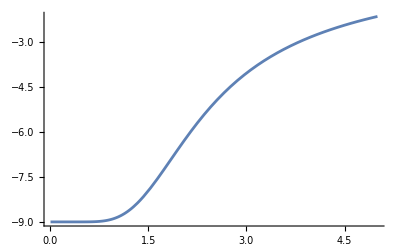

```mathematica
Plot[AvgEnergyCayleyGraphS3/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.1.5 | Energy Variance:

```mathematica
EnergyVarCayleyGraphS3=CalculateVarianceEnergy[ZCayleyGraphS3]//FullSimplify
```

(3 J^2 (34-52 Cosh[2 J β]+39 Cosh[4 J β]+3 Cosh[8 J β]+16 Sinh[2 J β]-18 Sinh[4 J β]-3 Sinh[8 J β]))/((1+Cosh[2 J β]) (-3+3 Cosh[2 J β]-2 Cosh[4 J β]+Sinh[4 J β])^2)

General::munfl: 1/((-4.61082×10^171)^2) is too small to represent as a normalized machine number; precision may be lost.

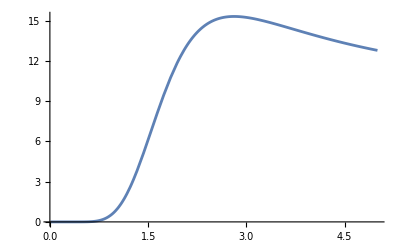

-Graphics-

```mathematica
Plot[EnergyVarCayleyGraphS3/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.1.6 | Free Energy:

```mathematica
FreeECayleyGraphS3=CalculateFreeEnergy[ZCayleyGraphS3]//FullSimplify
```

-Log[-32 ⅇ^(2 J β) Cosh[J β]^3 (-3+3 Cosh[2 J β]-2 Cosh[4 J β]+Sinh[4 J β])]/β

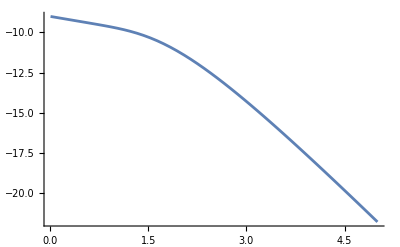

```mathematica
Plot[FreeECayleyGraphS3/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.1.7 | Entropy:

```mathematica
SCayleyGraphS3=CalculateEntropy[ZCayleyGraphS3]//FullSimplify
```

-2 J β+Log[-32 ⅇ^(2 J β) Cosh[J β]^3 (-3+3 Cosh[2 J β]-2 Cosh[4 J β]+Sinh[4 J β])]-(2 J β (2 Cosh[4 J β]+3 Sinh[2 J β]-4 Sinh[4 J β]))/(-3+3 Cosh[2 J β]-2 Cosh[4 J β]+Sinh[4 J β])-3 J β Tanh[J β]

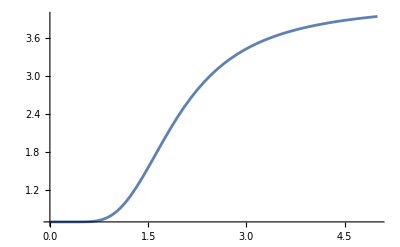

```mathematica
Plot[SCayleyGraphS3/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.2 | Ising-Like Spins for Cayley Graph of S_4

## Section 3.2.1 | Generating the Cayley Graph of S_4

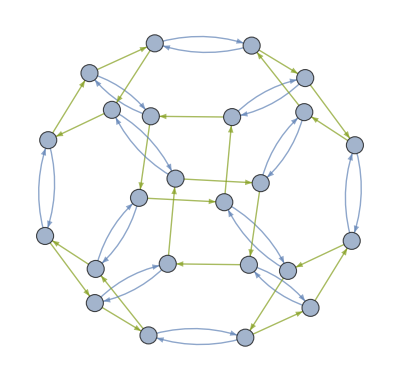

```mathematica
CayleyGraph[SymmetricGroup[4],VertexLabels->Placed["Name",Center],VertexSize->0.5]
```

## Section 3.2.2 | Hamiltonian

```mathematica
HamiltonianCayleyGraphS4=-J(
s[1](s[7]+s[10]+s[19])+
s[2](s[8]+s[9]+s[20])+
s[3](s[9]+s[12]+s[21])+
s[4](s[10]+s[11]+s[22])+
s[5](s[7]+s[11]+s[23])+
s[6](s[8]+s[12]+s[24])+
s[7](s[5]+s[16])+
s[8](s[15])+
s[9](s[18])+
s[10](s[17])+
s[11](s[13])+
s[12](s[14])+
s[13](s[15]+s[22])+
s[14](s[16]+s[21])+
s[15](s[24])+
s[16](s[23])+
s[17](s[18]+s[19])+
s[18](s[20])+
s[19](s[21])+
s[20](s[22])+
s[21](0)+
s[22](0)+
s[23](s[24])+
s[24](0)
)
```

-J (s[11] s[13]+s[12] s[14]+s[8] s[15]+s[7] (s[5]+s[16])+s[10] s[17]+s[9] s[18]+s[1] (s[7]+s[10]+s[19])+s[17] (s[18]+s[19])+s[18] s[20]+s[2] (s[8]+s[9]+s[20])+s[19] s[21]+s[3] (s[9]+s[12]+s[21])+s[14] (s[16]+s[21])+s[20] s[22]+s[4] (s[10]+s[11]+s[22])+s[13] (s[15]+s[22])+s[16] s[23]+s[5] (s[7]+s[11]+s[23])+s[15] s[24]+s[23] s[24]+s[6] (s[8]+s[12]+s[24]))

## Section 3.2.3 | Partition Function:

```mathematica
ZCayleyGraphS4=PartitionFunctionForIsingSpins[HamiltonianCayleyGraphS4,24,"Verbose"->False]//FullSimplify
```

$Aborted

```mathematica
ZCayleyGraphS4
```

8192 Cosh[J β]^11 (-15229+30420 Cosh[2 J β]-25852 Cosh[4 J β]+21571 Cosh[6 J β]-15561 Cosh[8 J β]+10866 Cosh[10 J β]-6716 Cosh[12 J β]+3861 Cosh[14 J β]-1903 Cosh[16 J β]+799 Cosh[18 J β]-264 Cosh[20 J β]+66 Cosh[22 J β]-11 Cosh[24 J β]+Cosh[26 J β])

```mathematica
Cosh[J β]^11 (-8192 15229+8192 30420 Cosh[2 J β]-8192 25852 Cosh[4 J β]+8192 21571 Cosh[6 J β]-8192 15561 Cosh[8 J β]+8192 10866 Cosh[10 J β]-8192 6716 Cosh[12 J β]+8192 3861 Cosh[14 J β]-8192 1903 Cosh[16 J β]+8192 799 Cosh[18 J β]-8192 264 Cosh[20 J β]+8192 66 Cosh[22 J β]-8192 11 Cosh[24 J β]+8192Cosh[26 J β])
```

Cosh[J β]^11 (-124755968+249200640 Cosh[2 J β]-211779584 Cosh[4 J β]+176709632 Cosh[6 J β]-127475712 Cosh[8 J β]+89014272 Cosh[10 J β]-55017472 Cosh[12 J β]+31629312 Cosh[14 J β]-15589376 Cosh[16 J β]+6545408 Cosh[18 J β]-2162688 Cosh[20 J β]+540672 Cosh[22 J β]-90112 Cosh[24 J β]+8192 Cosh[26 J β])

Try to not simplify again:

```mathematica
PartitionFunctionForIsingSpins[HamiltonianCayleyGraphS4,24,"Verbose"->False]
```

2 ⅇ^(-37 J β)+44 ⅇ^(-31 J β)+80 ⅇ^(-29 J β)+176 ⅇ^(-27 J β)+946 ⅇ^(-25 J β)+3090 ⅇ^(-23 J β)+8158 ⅇ^(-21 J β)+21700 ⅇ^(-19 J β)+54296 ⅇ^(-17 J β)+120800 ⅇ^(-15 J β)+243396 ⅇ^(-13 J β)+449858 ⅇ^(-11 J β)+753774 ⅇ^(-9 J β)+1136398 ⅇ^(-7 J β)+1548910 ⅇ^(-5 J β)+1913832 ⅇ^(-3 J β)+2133148 ⅇ^(-J β)+2133148 ⅇ^(J β)+1913832 ⅇ^(3 J β)+1548910 ⅇ^(5 J β)+1136398 ⅇ^(7 J β)+753774 ⅇ^(9 J β)+449858 ⅇ^(11 J β)+243396 ⅇ^(13 J β)+120800 ⅇ^(15 J β)+54296 ⅇ^(17 J β)+21700 ⅇ^(19 J β)+8158 ⅇ^(21 J β)+3090 ⅇ^(23 J β)+946 ⅇ^(25 J β)+176 ⅇ^(27 J β)+80 ⅇ^(29 J β)+44 ⅇ^(31 J β)+2 ⅇ^(37 J β)

```mathematica
ZCayleyGraphS4//Expand
```

-124755968 Cosh[J β]^11+249200640 Cosh[J β]^11 Cosh[2 J β]-211779584 Cosh[J β]^11 Cosh[4 J β]+176709632 Cosh[J β]^11 Cosh[6 J β]-127475712 Cosh[J β]^11 Cosh[8 J β]+89014272 Cosh[J β]^11 Cosh[10 J β]-55017472 Cosh[J β]^11 Cosh[12 J β]+31629312 Cosh[J β]^11 Cosh[14 J β]-15589376 Cosh[J β]^11 Cosh[16 J β]+6545408 Cosh[J β]^11 Cosh[18 J β]-2162688 Cosh[J β]^11 Cosh[20 J β]+540672 Cosh[J β]^11 Cosh[22 J β]-90112 Cosh[J β]^11 Cosh[24 J β]+8192 Cosh[J β]^11 Cosh[26 J β]

## Section 3.2.4 | Average Energy:

```mathematica
AvgEnergyCayleyGraphS4=CalculateAverageEnergy[ZCayleyGraphS4]//FullSimplify
```

J ((4 (10 Sinh[2 J β]-13 Sinh[4 J β]+6 Sinh[6 J β]-2 Sinh[8 J β]))/(14-20 Cosh[2 J β]+13 Cosh[4 J β]-4 Cosh[6 J β]+Cosh[8 J β])-(2 (410 Sinh[2 J β]-438 Sinh[4 J β]+714 Sinh[6 J β]-488 Sinh[8 J β]+470 Sinh[10 J β]-318 Sinh[12 J β]+175 Sinh[14 J β]-56 Sinh[16 J β]+9 Sinh[18 J β]))/(-111+410 Cosh[2 J β]-219 Cosh[4 J β]+238 Cosh[6 J β]-122 Cosh[8 J β]+94 Cosh[10 J β]-53 Cosh[12 J β]+25 Cosh[14 J β]-7 Cosh[16 J β]+Cosh[18 J β])-11 Tanh[J β])

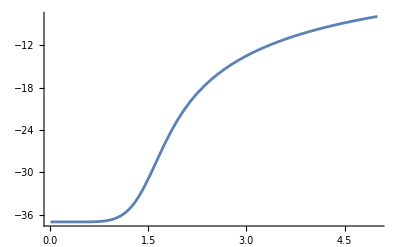

```mathematica
Plot[AvgEnergyCayleyGraphS4/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.2.5 | Energy Variance:

```mathematica
EnergyVarCayleyGraphS4=CalculateVarianceEnergy[ZCayleyGraphS4]//FullSimplify
```

(J^2 (33974111201-66255837296 Cosh[2 J β]+61909533680 Cosh[4 J β]-54990369512 Cosh[6 J β]+46750662822 Cosh[8 J β]-37741856536 Cosh[10 J β]+29085120156 Cosh[12 J β]-21242513776 Cosh[14 J β]+14758685838 Cosh[16 J β]-9695063384 Cosh[18 J β]+6036211616 Cosh[20 J β]-3544427572 Cosh[22 J β]+1965929031 Cosh[24 J β]-1025547356 Cosh[26 J β]+502719798 Cosh[28 J β]-229755368 Cosh[30 J β]+97081227 Cosh[32 J β]-37305320 Cosh[34 J β]+12803994 Cosh[36 J β]-3823612 Cosh[38 J β]+965715 Cosh[40 J β]-197492 Cosh[42 J β]+30980 Cosh[44 J β]-3320 Cosh[46 J β]+198 Cosh[48 J β]) Sech[J β]^2)/(2 (-15229+30420 Cosh[2 J β]-25852 Cosh[4 J β]+21571 Cosh[6 J β]-15561 Cosh[8 J β]+10866 Cosh[10 J β]-6716 Cosh[12 J β]+3861 Cosh[14 J β]-1903 Cosh[16 J β]+799 Cosh[18 J β]-264 Cosh[20 J β]+66 Cosh[22 J β]-11 Cosh[24 J β]+Cosh[26 J β])^2)

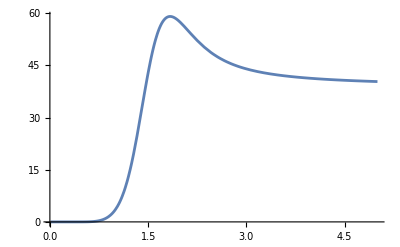

```mathematica
Plot[EnergyVarCayleyGraphS4/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.2.6 | Free Energy:

```mathematica
FreeECayleyGraphS4=CalculateFreeEnergy[ZCayleyGraphS4]//FullSimplify
```

-1/β Log[8192 Cosh[J β]^11 (-15229+30420 Cosh[2 J β]-25852 Cosh[4 J β]+21571 Cosh[6 J β]-15561 Cosh[8 J β]+10866 Cosh[10 J β]-6716 Cosh[12 J β]+3861 Cosh[14 J β]-1903 Cosh[16 J β]+799 Cosh[18 J β]-264 Cosh[20 J β]+66 Cosh[22 J β]-11 Cosh[24 J β]+Cosh[26 J β])]

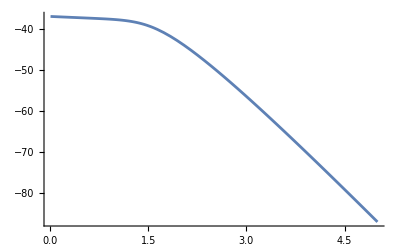

```mathematica
Plot[FreeECayleyGraphS4/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.2.7 | Entropy:

```mathematica
SCayleyGraphS4=CalculateEntropy[ZCayleyGraphS4]//FullSimplify
```

Log[8192 Cosh[J β]^11 (-15229+30420 Cosh[2 J β]-25852 Cosh[4 J β]+21571 Cosh[6 J β]-15561 Cosh[8 J β]+10866 Cosh[10 J β]-6716 Cosh[12 J β]+3861 Cosh[14 J β]-1903 Cosh[16 J β]+799 Cosh[18 J β]-264 Cosh[20 J β]+66 Cosh[22 J β]-11 Cosh[24 J β]+Cosh[26 J β])]+J β ((40 Sinh[2 J β]-52 Sinh[4 J β]+24 Sinh[6 J β]-8 Sinh[8 J β])/(14-20 Cosh[2 J β]+13 Cosh[4 J β]-4 Cosh[6 J β]+Cosh[8 J β])-(2 (410 Sinh[2 J β]-438 Sinh[4 J β]+714 Sinh[6 J β]-488 Sinh[8 J β]+470 Sinh[10 J β]-318 Sinh[12 J β]+175 Sinh[14 J β]-56 Sinh[16 J β]+9 Sinh[18 J β]))/(-111+410 Cosh[2 J β]-219 Cosh[4 J β]+238 Cosh[6 J β]-122 Cosh[8 J β]+94 Cosh[10 J β]-53 Cosh[12 J β]+25 Cosh[14 J β]-7 Cosh[16 J β]+Cosh[18 J β])-11 Tanh[J β])

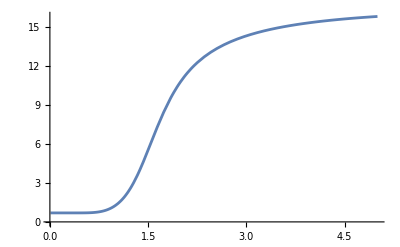

```mathematica
Plot[SCayleyGraphS4/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.3.1 | Generating the Cayley Graph of S_5

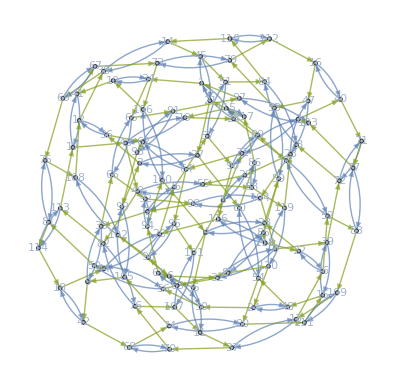

```mathematica
CayleyGraph[SymmetricGroup[5],VertexLabels->Placed["Name",Center],VertexSize->0.5]
```

## Section 3.3.2 | Hamiltonian

```mathematica
HamiltonianCayleyGraphS5=-J (
s[43] s[49]+s[44] s[50]+s[45] s[51]+s[46] s[52]+s[47] s[53]+s[48] s[54]+s[29] s[55]+s[30] s[56]+s[26] s[57]+s[25] s[58]+s[28] s[59]+s[27] s[60]+s[35] s[61]+s[36] s[62]+s[32] s[63]+s[31] s[64]+s[34] s[65]+s[33] s[66]+s[41] s[67]+s[42] s[68]+s[38] s[69]+s[37] s[70]+s[40] s[71]+s[39] s[72]+s[67] (s[69]+s[73])+s[68] (s[70]+s[74])+s[69] s[75]+s[70] s[76]+s[71] (s[72]+s[77])+s[72] s[78]+s[53] (s[59]+s[79])+s[54] (s[60]+s[80])+s[50] (s[56]+s[81])+s[49] (s[55]+s[82])+s[52] (s[58]+s[83])+s[51] (s[57]+s[84])+s[59] s[85]+s[60] s[86]+s[56] s[87]+s[55] s[88]+s[58] s[89]+s[57] s[90]+s[65] (s[66]+s[91])+s[66] s[92]+s[62] (s[64]+s[93])+s[61] (s[63]+s[94])+s[64] s[95]+s[63] s[96]+s[1] (s[25]+s[34]+s[97])+s[91] (s[93]+s[97])+s[2] (s[26]+s[33]+s[98])+s[92] (s[94]+s[98])+s[93] s[99]+s[3] (s[27]+s[36]+s[99])+s[94] s[100]+s[4] (s[28]+s[35]+s[100])+s[5] (s[29]+s[31]+s[101])+s[95] (s[96]+s[101])+s[96] s[102]+s[6] (s[30]+s[32]+s[102])+s[97] s[103]+s[7] (s[31]+s[40]+s[103])+s[77] (s[83]+s[103])+s[98] s[104]+s[8] (s[32]+s[39]+s[104])+s[78] (s[84]+s[104])+s[99] s[105]+s[9] (s[33]+s[42]+s[105])+s[74] (s[80]+s[105])+s[100] s[106]+s[10] (s[34]+s[41]+s[106])+s[73] (s[79]+s[106])+s[101] s[107]+s[11] (s[35]+s[37]+s[107])+s[76] (s[82]+s[107])+s[102] s[108]+s[12] (s[36]+s[38]+s[108])+s[75] (s[81]+s[108])+s[83] s[109]+s[13] (s[37]+s[46]+s[109])+s[84] s[110]+s[14] (s[38]+s[45]+s[110])+s[80] s[111]+s[109] s[111]+s[15] (s[39]+s[48]+s[111])+s[79] s[112]+s[110] s[112]+s[16] (s[40]+s[47]+s[112])+s[82] s[113]+s[17] (s[41]+s[43]+s[113])+s[81] s[114]+s[113] s[114]+s[18] (s[42]+s[44]+s[114])+s[19] (s[25]+s[43]+s[115])+s[89] (s[90]+s[115])+s[90] s[116]+s[20] (s[26]+s[44]+s[116])+s[115] s[117]+s[21] (s[27]+s[45]+s[117])+s[86] (s[88]+s[117])+s[116] s[118]+s[22] (s[28]+s[46]+s[118])+s[85] (s[87]+s[118])+s[88] s[119]+s[23] (s[29]+s[47]+s[119])+s[87] s[120]+s[119] s[120]+s[24] (s[30]+s[48]+s[120])
);
```

## Section 3.4.3 | Partition Function:

```mathematica
ZCayleyGraphS5=PartitionFunctionForIsingSpins[HamiltonianCayleyGraphS5,120,"Verbose"->False]//FullSimplify
```

Tuples::toomany: The length of the output of Tuples[{-1,1},120] should be a machine integer.

Thread::tdlen: Objects of unequal length in {s[1],s[2],s[3],s[4],s[5],s[6],s[7],s[8],s[9],s[10],«110»}→{-1,1} cannot be combined.

Tuples::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of Tuples[ⅇ^(J β (s[43] s[49]+s[44] s[50]+s[45] s[51]+s[46] s[52]+s[47] s[53]+s[48] s[54]+s[29] s[55]+s[30] s[56]+s[26] s[57]+s[25] s[58]+«98»)),ⅇ^(2592000 J β)].

$Aborted

## Section 3.4.4 | Average Energy:

```mathematica
AvgEnergyCayleyGraphS5=CalculateAverageEnergy[ZCayleyGraphS5]//FullSimplify
```

$Aborted

```mathematica
Plot[AvgEnergyCayleyGraphS4/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.4.5 | Energy Variance:

```mathematica
EnergyVarCayleyGraphS5=CalculateVarianceEnergy[ZCayleyGraphS5]//FullSimplify
```

```mathematica
Plot[EnergyVarCayleyGraphS5/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.4.6 | Free Energy:

```mathematica
FreeECayleyGraphS5=CalculateFreeEnergy[ZCayleyGraphS5]//FullSimplify
```

```mathematica
Plot[FreeECayleyGraphS5/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.4.7 | Entropy:

```mathematica
SCayleyGraphS5=CalculateEntropy[ZCayleyGraphS5]//FullSimplify
```

```mathematica
Plot[SCayleyGraphS5/.J->1/.β->1/T,{T,0.01,5}]
```

## Section 3.5.1 | Generating the Cayley Graph of S_6

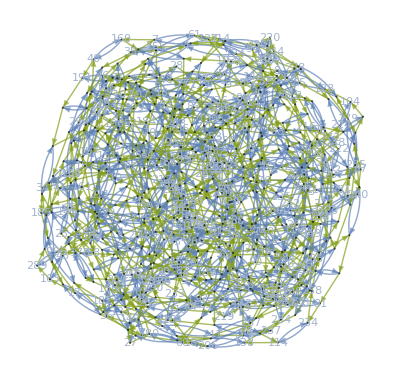

```mathematica
CayleyGraph[SymmetricGroup[6],VertexLabels->Placed["Name",Center],VertexSize->0.5]
```

## Section 3.X.1 | Analysis of Cayley Graph of S_n

Now, we make some guesses:

```mathematica
ZCayleyGraphSN=(constant Cosh[β J]^n+ Sum[b[i] Cosh[c[i] β J]^(n+1),{i,1,p}])
```

constant Cosh[J β]^n+∑_(i=1)^p b[i] Cosh[J β c[i]]^(1+n)

```mathematica
AvgEnergyCayleyGraphSN=CalculateAverageEnergy[ZCayleyGraphSN]//FullSimplify
```

-(∑_(i=1)^p J b[i] c[i] Sinh[J β c[i]])/(constant+∑_(i=1)^p b[i] Cosh[J β c[i]])-J n Tanh[J β]

```mathematica
EnergyVarCayleyGraphSN=CalculateVarianceEnergy[ZCayleyGraphSN]//FullSimplify
```

((constant+∑_(i=1)^p b[i] Cosh[J β c[i]]) (J^2 n Sech[J β]^2 (constant+∑_(i=1)^p b[i] Cosh[J β c[i]])+∑_(i=1)^p J^2 b[i] c[i]^2 Cosh[J β c[i]])-(∑_(i=1)^p J b[i] c[i] Sinh[J β c[i]])^2)/((constant+∑_(i=1)^p b[i] Cosh[J β c[i]])^2)

```mathematica
FreeECayleyGraphSN=CalculateFreeEnergy[ZCayleyGraphSN]//FullSimplify
```

-Log[Cosh[J β]^n (constant+∑_(i=1)^p b[i] Cosh[J β c[i]])]/β

```mathematica
SCayleyGraphSN=CalculateEntropy[ZCayleyGraphSN]//FullSimplify
```

Log[Cosh[J β]^n (constant+∑_(i=1)^p b[i] Cosh[J β c[i]])]-(β ∑_(i=1)^p J b[i] c[i] Sinh[J β c[i]])/(constant+∑_(i=1)^p b[i] Cosh[J β c[i]])-J n β Tanh[J β]